This notebook imports dat files, and plots energy eigenvalues and LDoS of projected Topo SC

```mathematica
(*-----------------------------------------------------------------------------------------------------------------------------*)
```

```mathematica
datFileEnergylocation="/data/topo_super/dislocation/energies/";
datFileLDOSlocation="/data/topo_super/dislocation/LDOS/";
datfilePBCName="t0=1.0_t=1.0_m_0=0.0_mu=0.0_Delta=2.5_x_periodic=1_y_periodic=1_L=60_l1=15_l2=30_mlattice=30_m=0.6180339887498949_c1=-5_c2=2";
datfileOBCName="t0=1.0_t=1.0_m_0=0.0_mu=0.0_Delta=0.5_x_periodic=1_y_periodic=1_L=60_l1=15_l2=30_mlattice=30_m=0.6180339887498949_c1=-5_c2=2";
```

```mathematica
StringJoin[datFileEnergylocation,datfilePBCName];
```

```mathematica
Clear[dataEnergyPBC,dataEnergyOBC]
```

```mathematica
(** Change the filenames accordingly and import the dat files **)
```

```mathematica
dataEnergyPBC=Flatten[Import[StringJoin[ParentDirectory[NotebookDirectory[]],datFileEnergylocation,datfilePBCName,".csv"]]];
```

```mathematica
dataEnergyOBC=Flatten[Import[StringJoin[ParentDirectory[NotebookDirectory[]],datFileEnergylocation,datfileOBCName,".csv"]]];
```

```mathematica
Clear[Lattice];
```

```mathematica
Lattice=Table[{j,0},{j,1,Dimensions[dataEnergyOBC][[1]]/4}];
```

```mathematica
largestX = Dimensions[Lattice][[1]]
```

404

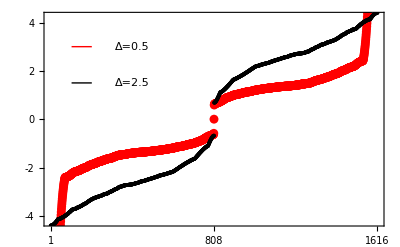

```mathematica
plt1=Show[
ListPlot[dataEnergyOBC,Frame-> True,Axes-> False,PlotRange-> {{0,4*largestX},{-4.25,4.25}},PlotStyle-> {Red,PointSize[0.016]},FrameStyle-> {{Black,Thick},{Black,Thick},{Black,Thick},{Black,Thick}},FrameTicks-> {{{-4,-2,0,2,4},None},{{1,2*largestX,4*largestX},None}},BaseStyle-> 18],

ListPlot[dataEnergyPBC,PlotStyle-> {Black,PointSize[0.007]}],

Plot[3,{x,largestX-200,largestX-300},PlotStyle-> {Thick,Red}],
Plot[1.5,{x,largestX-200,largestX-300},PlotStyle-> {Thick,Black}],

Epilog-> {Inset["Δ=0.5",{largestX,3}],Inset["Δ=2.5",{largestX,1.5}]}
]
```

```mathematica
Export[StringJoin[ParentDirectory[NotebookDirectory[]],datFileEnergylocation,datfileOBCName,".pdf"],plt1];
```

```mathematica
(*-----------------------------------------------------------------------------------------------------------------------------*)
```

```mathematica
(*-----------------------------------------------------------------------------------------------------------------------------*)
```

```mathematica
(*-----------------------------------------------------------------------------------------------------------------------------*)
```

```mathematica
Clear[dataLDoSPBC,dataLDoSOBC,colorfunc]
```

```mathematica
(** Change the filenames accordingly and import the dat files **)
```

```mathematica
dataLDoSPBCdat=Flatten[Import[StringJoin[ParentDirectory[NotebookDirectory[]],datFileLDOSlocation,datfilePBCName,".csv"]]];
```

```mathematica
dataLDoSPBC=Table[{nn,0,dataLDoSPBCdat[[nn]]},{nn,1,largestX}];
```

```mathematica
dataLDoSOBCdat=Flatten[Import[StringJoin[ParentDirectory[NotebookDirectory[]],datFileLDOSlocation,datfileOBCName,".csv"]]];
```

```mathematica
dataLDoSOBC=Table[{nn,0,dataLDoSOBCdat[[nn]]},{nn,1,largestX}];
```

```mathematica
colorfunc=Function[{v,vmax},Hue[0.5+0.5*v/vmax,1,1.0-0.3 v/vmax,v/vmax]];
```

```mathematica
rngOld={0,Max[#]}&@dataLDoSOBC[[All,3]]
```

{0,0.368765}

```mathematica
rng={0,0.38}
```

{0,0.38}

```mathematica
P1=BarLegend[{colorfunc[#,rng[[2]]]&,{0,rng[[2]]}},LabelStyle->{Black,FontSize-> 15},Ticks-> {{0,"0.0"},{rng[[2]]/2,"3.25"},{rng[[2]]-10^-3,"6.5"}}]
```

```mathematica
(** Crop the image appropriately and put the numbers in inkscape **)
```

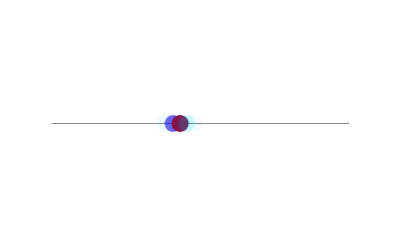

```mathematica
plt2=Show[
ListPlot[Lattice,Frame-> False,Axes-> False,PlotStyle-> {Black,PointSize[0.001]},PlotRange-> {{-20,largestX+20},{-2,2}}],
Graphics[{Opacity[0.1],
PointSize[0.03],colorfunc[#[[3]],rng[[2]]],Point[#[[1;;2]]]}&/@dataLDoSOBC,
BaseStyle-> 18
]

]
```

```mathematica
Export[StringJoin[ParentDirectory[NotebookDirectory[]],datFileLDOSlocation,datfileOBCName,".pdf"],plt2]
```

/home/archisman/Documents/GitHub/lattices-julia/data/topo_super/dislocation/LDOS/t0=1.0_t=1.0_m_0=0.0_mu=0.0_Delta=0.5_x_periodic=1_y_periodic=1_L=60_l1=15_l2=30_mlattice=30_m=0.6180339887498949_c1=-5_c2=2.pdf